```mathematica
ClearAll["Global`*"]
```

```mathematica
L=2*2.2;
h=0.41;
μ=0.001;
```

```mathematica
ϵ=1*^-3;
```

```mathematica
(*height profile of the manifold*)
```

```mathematica
z[y_]:=(2)y(h-y)/h^2 (y-h/24) /h
```

```mathematica
(*sg = Sqrt[Det[g_{ij}]]*)
```

```mathematica
sg[y_]:=Sqrt[1+(z'[y])^2]
```

```mathematica
B=Δ/μ*NIntegrate[sg[v]sg[u] If[u<=v,1,0],{u,0,h},{v,0,h}]/NIntegrate[sg[u],{u,0,h}]
```

364.764 Δ

```mathematica
CC=B μ/Δ
```

0.364764

```mathematica
v[y_]:=Δ/μ(NIntegrate[sg[v]sg[u] If[u<=v,1,0],{u,0,h},{v,0,y}]-CC NIntegrate[sg[v],{v,0,y}] )
vflat[y_]:=Δflat y (h-y)
```

```mathematica
Clear[Δ]
```

```mathematica
(*here put the latest snapshot of v generated by the dynamics*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/channel_with_cylinder_curved_cn/solution/snapshots/csv/v_n512.csv"];
t=Drop[t,{1}]
```

```mathematica
For[vnum={};i=1, i<= Length[t], i++,
If[Abs[t[[i,4]]-L]<ϵ,AppendTo[vnum,{t[[i,5]],t[[i,1]]}]];
]
```

```mathematica
vnum
```

{{0.41,6.55534×10^-9},{0.364444,0.165675},{0.387222,0.105445},{0.318889,0.213657},{0.341667,0.197383},{0.273333,0.225827},{0.296111,0.221781},{0.227778,0.228442},{0.250556,0.228308},{0.182222,0.216358},{0.205,0.224895},{0.136667,0.179932},{0.159444,0.201211},{0.0911111,0.121902},{0.113889,0.152809},{0.0455556,0.0585211},{0.0683333,0.0895908},{0.,1.81137×10^-8},{0.0227778,0.0271754}}

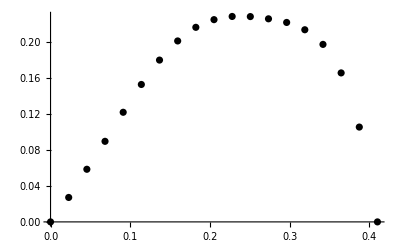

```mathematica
plotnum=ListPlot[vnum,PlotStyle->Black]
```

```mathematica
(*pick an index i0 in the middle of vnum*)
i0=Round[Length[vnum]/2];
y0=vnum[[i0,1]]
v0=vnum[[i0,2]]
```

0.182222

0.216358

```mathematica
sol=Flatten[Solve[v[y0]==v0,Δ]]
solflat=Flatten[Solve[vflat[y0]==v0,Δflat]]
```

{Δ→-0.0034374}

{Δflat→5.21266}

```mathematica
Δ=Δ/.sol
Δflat=Δflat/.solflat
```

-0.0034374

5.21266

```mathematica
v[h/2]
```

0.224917

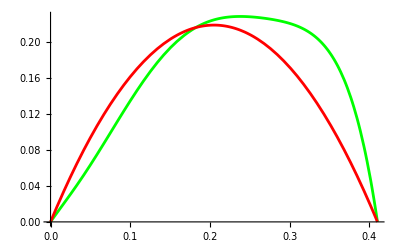

```mathematica
Show[Plot[v[y],{y,0,h}, PlotStyle->Green],Plot[vflat[y],{y,0,h}, PlotStyle->Red]]
```

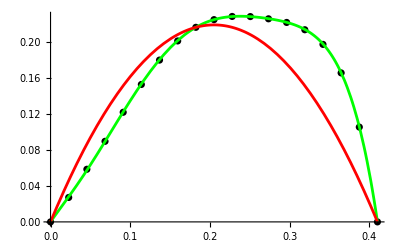

```mathematica
Show[plotnum,Plot[v[y],{y,0,h}, PlotStyle->Green],Plot[vflat[y],{y,0,h}, PlotStyle->Red]]
```